```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SecSusceptHeight={{4,1.310617,0.00520}, {8, 4.002690545,0.029074},{16,12.953, 0.1056}, {32, 41.5689916, 1.2237}};
SecSusceptHeightPoints = Table[Log[{SecSusceptHeight[[i]][[1]],SecSusceptHeight[[i]][[2]]}], {i, 1, Length[SecSusceptHeight]}];
SecSusceptHeightErrors = Table[SecSusceptHeight[[i]][[3]]/SecSusceptHeight[[i]][[2]],{i,1,Length[SecSusceptHeight]}];
SecSusceptWidth={{4, 0.0541,0.00049}, {8,0.026319, 0.000420}, {16,0.01256, 0.000278},{32, 0.006609, 0.000726}};
SecSusceptWidthPoints = Table[Log[{SecSusceptWidth[[i]][[1]],SecSusceptWidth[[i]][[2]]}], {i, 1, Length[SecSusceptWidth]}];
SecSusceptWidthErrors = Table[SecSusceptWidth[[i]][[3]]/SecSusceptWidth[[i]][[2]],{i,1,Length[SecSusceptWidth]}];
SecSusceptPos={{4, 0.14014395,0.00029}, {8, 0.166519, 0.000259}, {16,0.1786131974,0.00017583},{32, 0.18383, 0.0003149}};
SecSusceptPosPoints = Table[{SecSusceptPos[[i]][[1]],SecSusceptPos[[i]][[2]]}, {i, 1, Length[SecSusceptPos]}];
SecSusceptPosErrors = Table[SecSusceptPos[[i]][[3]],{i,1,Length[SecSusceptPos]}];
```

```mathematica
SecSusceptHeightFit = NonlinearModelFit[SecSusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SecSusceptHeightErrors^2];
```

```mathematica
SecSusceptWidthFit = NonlinearModelFit[SecSusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SecSusceptWidthErrors^2];
```

```mathematica
SecSusceptPosFit = NonlinearModelFit[SecSusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SecSusceptPosErrors^2];
```

```mathematica
SusceptHeight={{4,1.433738,0.0050138}, {8, 4.2354,0.015263},{16,13.2055966, 0.1015},{32, 42.582, 0.38578}, {64,141.934,2.34606},{128,472.449,8.02534}};
SusceptHeight={{4,1.433738,0.0050138}, {8, 4.2354,0.015263},{16,13.2055966, 0.1015},{32, 42.582, 0.38578}};
SusceptHeightPoints = Table[Log[{SusceptHeight[[i]][[1]],SusceptHeight[[i]][[2]]}], {i, 1, Length[SusceptHeight]}];
SusceptHeightErrors = Table[SusceptHeight[[i]][[3]]/SusceptHeight[[i]][[2]],{i,1,Length[SusceptHeight]}];
SusceptWidth={{4, 0.12460,0.000796 }, {8, 0.069091, 0.0006276}, {16,0.03763, 0.00047077}, {32, 0.01954, 0.0004501},{64, 0.00994924, 0.000361},{128,0.004800,0.000249}};
SusceptWidth={{4, 0.12460,0.000796 }, {8, 0.069091, 0.0006276}, {16,0.03763, 0.00047077}, {32, 0.01954, 0.0004501}};
SusceptWidthPoints = Table[Log[{SusceptWidth[[i]][[1]],SusceptWidth[[i]][[2]]}], {i, 1, Length[SusceptWidth]}];
SusceptWidthErrors = Table[SusceptWidth[[i]][[3]]/SusceptWidth[[i]][[2]],{i,1,Length[SusceptWidth]}];
SusceptPos={{4, 0.17852967,0.0006346}, {8, 0.3156, 0.0003554}, {16,0.377971,0.000862583},{32,0.41023,0.000250 },{64,0.425546,0.000219},{128,0.433118,0.00012139 }};
SusceptPosPoints = Table[{SusceptPos[[i]][[1]],SusceptPos[[i]][[2]]}, {i, 1, Length[SusceptPos]}];
SusceptPosErrors = Table[SusceptPos[[i]][[3]],{i,1,Length[SusceptPos]}];
```

```mathematica
SusceptHeightFit = NonlinearModelFit[SusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SusceptHeightErrors^2];
```

```mathematica
SusceptWidthFit = NonlinearModelFit[SusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SusceptWidthErrors^2];
```

```mathematica
SusceptPosFit = NonlinearModelFit[SusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SusceptPosErrors^2];
```

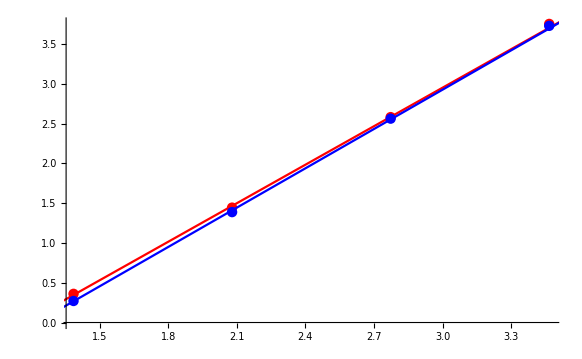

```mathematica
Show[
ErrorListPlot[
Table[{SusceptHeightPoints[[i]][[1]],SusceptHeightPoints[[i]][[2]], SusceptHeightErrors[[i]]},{i,1,Length[SusceptHeightPoints]}], PlotStyle->{Red}],
Plot[SusceptHeightFit[x],{x,0,5},PlotRange->Full,PlotStyle->{Red},PlotLegends->Placed[{"Nearest neighbour"},{Right,Bottom}]],
ErrorListPlot[
Table[{SecSusceptHeightPoints[[i]][[1]],SecSusceptHeightPoints[[i]][[2]], SecSusceptHeightErrors[[i]]},{i,1,Length[SecSusceptHeightPoints]}], PlotStyle->{Blue}],
Plot[SecSusceptHeightFit[x],{x,0,5},PlotRange->Full, PlotStyle->{Blue}, PlotLegends->Placed[{"2nd Nearest neighbour"},{Right,Bottom}]]
]
```

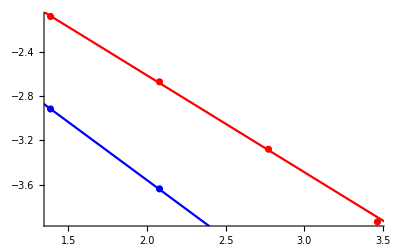

```mathematica
Show[
ErrorListPlot[
Table[{SusceptWidthPoints[[i]][[1]],SusceptWidthPoints[[i]][[2]], SusceptWidthErrors[[i]]},{i,1,Length[SusceptWidthPoints]}], PlotStyle->{Red}],
Plot[SusceptWidthFit[x],{x,0,10},PlotStyle->{Red},PlotLegends->Placed[{"Nearest neighbour"},{Right,Top}]],
ErrorListPlot[
Table[{SecSusceptWidthPoints[[i]][[1]],SecSusceptWidthPoints[[i]][[2]], SecSusceptWidthErrors[[i]]},{i,1,Length[SecSusceptWidthPoints]}], PlotStyle->{Blue}],
Plot[SecSusceptWidthFit[x],{x,0,10}, PlotStyle->{Blue}, PlotLegends->Placed[{"2nd Nearest neighbour"},{Right,Top}]]
]
```

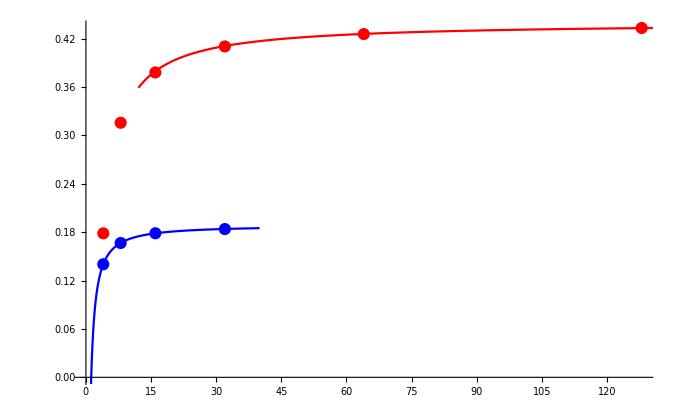

```mathematica
Show[
ErrorListPlot[
Table[{SusceptPosPoints[[i]][[1]],SusceptPosPoints[[i]][[2]], SusceptPosErrors[[i]]},{i,1,Length[SusceptPosPoints]}], PlotStyle->{Red}],
Plot[SusceptPosFit[x],{x,0,150},PlotStyle->{Red},PlotLegends->Placed[{"Nearest neighbour"},{Right,Center}]],
ErrorListPlot[
Table[{SecSusceptPosPoints[[i]][[1]],SecSusceptPosPoints[[i]][[2]], SecSusceptPosErrors[[i]]},{i,1,Length[SecSusceptPosPoints]}], PlotStyle->{Blue}],
Plot[SecSusceptPosFit[x],{x,0,40}, PlotStyle->{Blue}, PlotLegends->Placed[{"2nd Nearest neighbour"},{Right,Center}],PlotRange->Full]
]
```